```mathematica
e[k_,h_] = 2*Sqrt[1+h^2-2*h*Cos[k]]
```

2 √(1+h^2-2 h Cos[k])

```mathematica
f[h_,t_,L_]:=1/L Sum[Cos[ 2*t*e[((2*i-1)*π)/L,h] ],{i,1,L/2}]
```

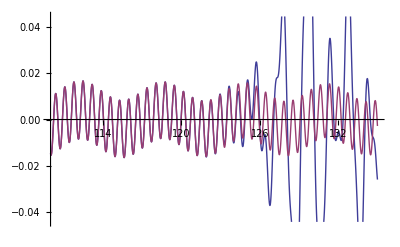

```mathematica
Plot[{f[1.25,t,512],f[1.25,t,1024]},{t,110,135}]
```

```mathematica
(*Magnetization*)
```

```mathematica
term[h0_,h_,t_,L_,k_]=-2(Cos[k]-h0)/e[k,h0]-8((h0-h)Sin[k]^2)/(e[k,h]^2*e[k,h0])(1-Cos[ 2*t*e[k,h] ])
f2[h0_,h_,t_,L_]:=2/L Sum[term[h0,h,t,L,((2*i-1)*π)/L],{i,1,L/2}]
```

-(-h0+Cos[k])/(√(1+h0^2-2 h0 Cos[k]))-((-h+h0) (1-Cos[4 t √(1+h^2-2 h Cos[k])]) Sin[k]^2)/((1+h^2-2 h Cos[k]) √(1+h0^2-2 h0 Cos[k]))

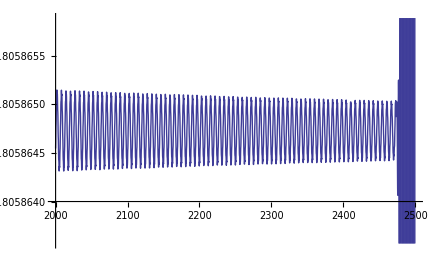

```mathematica
Plot[{f2[1.5,1.25,t,10000]},{t,2000,2500}]
```